```mathematica
(* Brownian Motion and Brownian Bridge *)

Clear[BM,BB]
BM[n_,rn_,t_]:=Module[{i},Sqrt[2]Sum[rn[[i]] Sin[(i-1/2)Pi t]/((i-1/2)Pi),{i,1,n}]]
BB[n_,rn_,t_]:=Module[{i},Sqrt[2]Sum[rn[[i]] Sin[i Pi t]/(i Pi),{i,1,n}]]
```

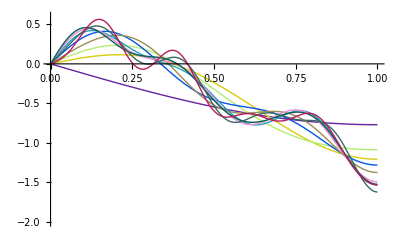

```mathematica
(* Initial example of refining a BM *)
n = 10;
sd = 35751;
SeedRandom[sd];
rn = RandomReal[NormalDistribution[0,1],n];

pltb=Table[Plot[BM[i,rn,t],{t,0,1},PlotStyle->RGBColor[RandomReal[UniformDistribution[{0,1}],3]]],{i,1,n}];
Show[pltb,PlotRange->{{0,1},{-2,0.6}}]
```

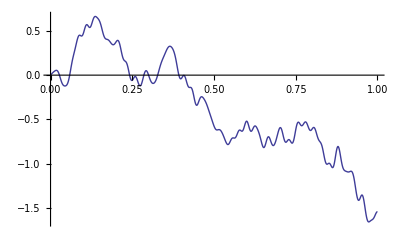

```mathematica
(* Let's plot a really high freq one next *)
n = 100;
sd = 35751;
SeedRandom[sd];
rn = RandomReal[NormalDistribution[0,1],n];
Plot[BM[n,rn,t],{t,0,1}]
```

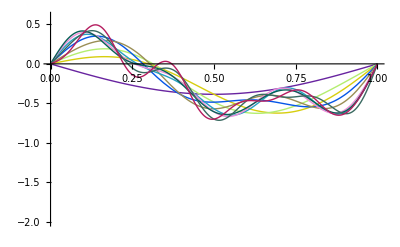

```mathematica
(* Let's try a Brownian Bridge next *)

n = 10;
sd = 35751;
SeedRandom[sd];
rn = RandomReal[NormalDistribution[0,1],n];

pltb=Table[Plot[BB[i,rn,t],{t,0,1},PlotStyle->RGBColor[RandomReal[UniformDistribution[{0,1}],3]]],{i,1,n}];
Show[pltb,PlotRange->{{0,1},{-2,0.6}}]
```

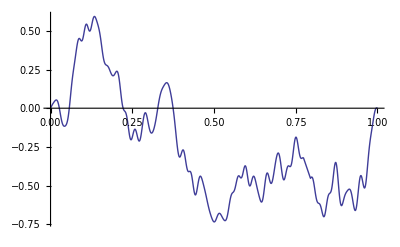

```mathematica
(* Next plot a high frequency BB *)
n = 100;
sd = 35751;
SeedRandom[sd];
rn = RandomReal[NormalDistribution[0,1],n];
Plot[BB[n,rn,t],{t,0,1}]
```

```mathematica
(* Now implement Sylvain's results for OU processes here *)
```